### I1

Breaking up the delta function

```mathematica
f[x_,p_]:=p-(4(1-x))/(2-x)^2
roots=Solve[f[x,p]==0,x]
```

{{x→(2 (-1-√(1-p)+p))/p},{x→(2 (-1+√(1-p)+p))/p}}

```mathematica
r1=x/.roots[[2]]
d1=FullSimplify[D[f[x,p],x]/.{x->r1}]
```

(2 (-1+√(1-p)+p))/p

2 (1+√(1-p))-(2+√(1-p)) p

```mathematica
r2=x/.roots[[1]]
d2=FullSimplify[D[f[x,p],x]/.{x->r2}]
```

(2 (-1-√(1-p)+p))/p

2-2 √(1-p)+(-2+√(1-p)) p

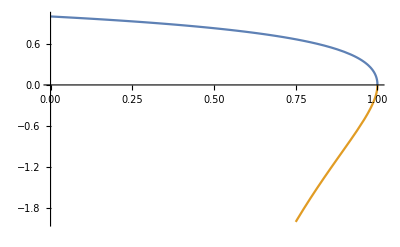

```mathematica
Plot[{r1/.{p->p1},r2/.{p->p1}},{p1,0,1},PlotRange->{-2,1}]
```

Setting up bounds of integration

```mathematica
Reduce[{(1-z)(2-r1)<1,0<p<1},p]
```

(0<z≤1/2&&0<p<4 z-4 z^2)||(z>1/2&&0<p<1)

```mathematica
Reduce[{1-r1>0,0<z<1/2},p]
```

0<z<1/2&&0<p≤1

Solving the integral

```mathematica
i1=1/Abs[d1] Assuming[{0<z<1/2,0<p<4 z-4 z^2},Integrate[(r1^2+x2^1)/((1-r1)(1-x2)),{x2,1-r1,z(2-r1)}]]
```

(p (p-2 (-1+√(1-p)) (-1+z))+(-8+8 √(1-p)+12 p-8 √(1-p) p-5 p^2) Log[2]+(-8+8 √(1-p)+12 p-8 √(1-p) p-5 p^2) Log[(-1+√(1-p)+p)/p]+(8-8 √(1-p)+4 (-3+2 √(1-p)) p+5 p^2) Log[1+(2 (-1+√(1-p)) z)/p])/(p (-2+2 √(1-p)+p) Abs[2 (1+√(1-p))-(2+√(1-p)) p])

### I2

```mathematica
Solve[z(2-r1)==1,p]
```

{{p→-4 (-z+z^2)}}

```mathematica
Reduce[{z(2-r1)<1,0<p<1},p]
```

(z≤1/2&&0<p<1)||(1/2<z<1&&0<p<4 z-4 z^2)

```mathematica
Reduce[1-r1>0,p]
```

0<p≤1

```mathematica
Reduce[{1-r1<z(2-r1),0<p<1},p]
```

(0<z≤1/2&&0<p<4 z-4 z^2)||(z>1/2&&0<p<1)

```mathematica
Reduce[{1-r1>z(2-r1),0<p<1},p]
```

(z≤0&&0<p<1)||(0<z<1/2&&4 z-4 z^2<p<1)

```mathematica
Solve[1-r1==z(2-r1),p]
```

{{p→-4 (-z+z^2)}}

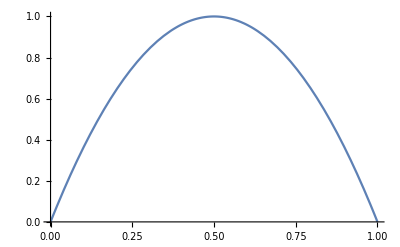

```mathematica
Plot[-4 (-z+z^2),{z,0,1}]
```

```mathematica
i2=1/Abs[d1] Assuming[{0<z<1/2,0<p<4 z-4 z^2},Integrate[(r1^2+x2^1)/((1-r1)(1-x2)),{x2,1-r1,z(2-r1)}]]
```

(p (p-2 (-1+√(1-p)) (-1+z))+(-8+8 √(1-p)+12 p-8 √(1-p) p-5 p^2) Log[2]+(-8+8 √(1-p)+12 p-8 √(1-p) p-5 p^2) Log[(-1+√(1-p)+p)/p]+(8-8 √(1-p)+4 (-3+2 √(1-p)) p+5 p^2) Log[1+(2 (-1+√(1-p)) z)/p])/(p (-2+2 √(1-p)+p) Abs[2 (1+√(1-p))-(2+√(1-p)) p])

### I5

```mathematica
g[x2_]:=p-(4(x1+x2-1))/(x1+x2)^2
```

```mathematica
roots5=Solve[g[x2]==0,x2];
s1=x2/.roots5[[2]]
s2=x2/.roots5[[1]]
```

(2+2 √(1-p)-p x1)/p

(2-2 √(1-p)-p x1)/p

```mathematica
sigma1=FullSimplify[g'[s1]]
sigma2=FullSimplify[g'[s2]]
```

-2+2 √(1-p)+2 p-√(1-p) p

-2 (1+√(1-p))+(2+√(1-p)) p

```mathematica
Reduce[{0<s1<1,0<x1<1,0<p<1},p]
Reduce[{0<s2<1,0<x1<1,0<p<1},p]
```

False

0<x1<1&&0<p<(4 x1)/(1+2 x1+x1^2)

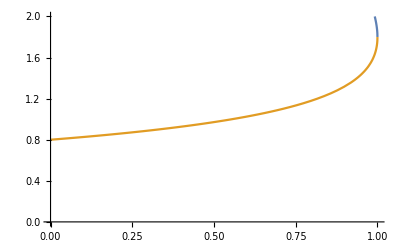

```mathematica
Plot[{s1/.{p->p1,x1->0.2},s2/.{p->p1,x1->0.2}},{p1,0,1},PlotRange->{0,2}]
```

```mathematica
Reduce[{s2+x1>1,0<p<1,0<x1<1},x1]
```

0<p<1&&0<x1<1

```mathematica
Reduce[{(2(1-z)(1-√(1-p)))/p<1,0<p<1},p]
```

(0<z≤1/2&&0<p<4 z-4 z^2)||(z>1/2&&0<p<1)

```mathematica
i5=1/Abs[sigma2] Assuming[{0<z<1/2,0<p<4 z-4 z^2},Integrate[(s2^2+x1^1)/((1-s2)(1-x1)),{x1,0,(2(1-z)(1-√(1-p)))/p}]]
```

(∫_0^((2 (1-√(1-p)) (1-z))/p) (x1+(2-2 √(1-p)-p x1)^2/p^2)/((1-x1) (1-(2-2 √(1-p)-p x1)/p))ⅆx1)/Abs[-2 (1+√(1-p))+(2+√(1-p)) p]

### Plot the results

```mathematica
Assuming[{0<p<1,0<z<1/2},FullSimplify[2i2+2i1]]
```

$Aborted

```mathematica
LogLinearPlot[(2i1+2i2+2i5)/.{p->p1,z->0.04},{p1,0.005,1},PlotRange->{0,15}]
```

$Aborted

```mathematica
f[x_]:=p-(4(1-x))/(2-x)^2
FullSimplify[f'[(2(p-1)+2 √(1-p))/p]]
```

2 (1+√(1-p))-(2+√(1-p)) p

```mathematica
Reduce[{(2-(2(p-1)+2 √(1-p))/p)(1-z)<1,0<p<1},p]
```

(0<z≤1/2&&0<p<4 z-4 z^2)||(z>1/2&&0<p<1)

```mathematica
FullSimplify[FullSimplify[Integrate[(r^2+x^2)/((1-r)(1-x)),x]/.{x->(2+2 √(1-p))/p(1-z),r->(2(p-1)+2 √(1-p))/p}]-FullSimplify[Integrate[(r^2+x^2)/((1-r)(1-x)),x]/.{x->1-(2+2 √(1-p))/p,r->(2(p-1)+2 √(1-p))/p}]]
```

1/(2 p (-2+2 √(1-p)+p))(12 (1+√(1-p)) p-3 p^2+8 (1+√(1-p)) (-2+z) z-4 p z (-1+√(1-p)+z)-2 (8-8 √(1-p)+p (-12+8 √(1-p)+5 p)) Log[-(2 (1+√(1-p)))/p]+2 (8-8 √(1-p)+p (-12+8 √(1-p)+5 p)) Log[-1-(2 (1+√(1-p)) (-1+z))/p])

```mathematica
Manipulate[Plot[%90,{p,0.001,1}],{z,0,1}]
```

```mathematica
r=(2(p-1)+2 √(1-p))/p;
Reduce[1-r>(2-r)(1-z),p]
```

(1/2<z≤1&&4 z-4 z^2<p≤1)||(z>1&&(4 z-4 z^2<p<0||0<p≤1))